## We convert the coefficient from the lattice style first order allpass fitler to the corresponding coefficients for a first order direct form filter

We derive the difference equation from the code in StageProcFPU.hpp in Laurent De Soras HIIR library:

    if(remaining == 1){
        const size_t last = numCoefficients - 1;
        const float  temp = (*sample0 - y[last]) * coef[last] + x[last];
        x[last] = *sample0;
        y[last] = temp;
        *sample0 = temp;
    }
    
    y[n] = (x[n] - y[n-1]) * c + x[n-1]

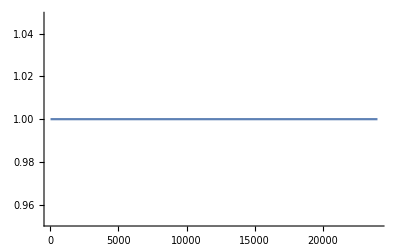

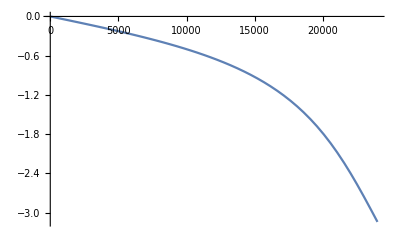

```mathematica
ha1[z_,c_]:=(z c + 1)/(z + c)
zz[ω_,sampleRate_]:=ⅇ^(ⅈ 2 π ω/sampleRate)
Plot[Abs[ha1[zz[ω,48000],0.5]],{ω,20,24000}]
Plot[Arg[ha1[zz[ω,48000],0.5]],{ω,20,24000}]
```

```mathematica
ha1[z,c1]ha1[z,c2]//ExpandNumerator//ExpandDenominator
```

(1+c1 z+c2 z+c1 c2 z^2)/(c1 c2+c1 z+c2 z+z^2)

```mathematica
BiquadAllpass[z_,c1_,c2_]:=(1+(c1+c2)z+c1 c2 z^2)/(c1 c2+(c1+c2) z+z^2)
BiquadAllpass[z,c1,c2]
```

(1+(c1+c2) z+c1 c2 z^2)/(c1 c2+(c1+c2) z+z^2)

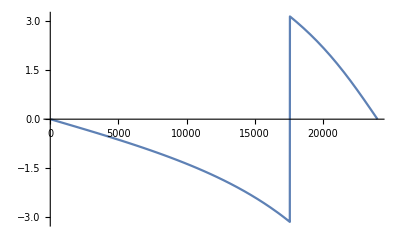

```mathematica
Plot[Arg[BiquadAllpass[zz[ω,48000],0.5,0.25]],{ω,20,24000}]
```